# Drugi kviz

Vsaka podnaloga je vredna 1 točko, razen če je pri podnalogi zapisano drugače. Skupno je moč doseči 20 točk.

## Naloga 1

a)  Definirajte funkcijo , ki sprejme naravni števili  in  in vrne matriko dimenzije , kjer se na vsakem mestu v matriki pojavi produkt indeksa stolpca in indeksa vrstice (začnemo šteti z 1).

```mathematica
A[n_,m_]:= Table[i+j,{i,1,n},{j,1,m}]
```

b) Pokažite, da je  simetrična matrika.

```mathematica
SymmetricMatrixQ[A[n,m]]
```

Table::iterb: Iterator {i,1,n} does not have appropriate bounds.

False

c) Izračunajte lastne vrednosti in lastne vektorje matrike .

```mathematica
Eigenvalues[A[10,10]]
Eigenvectors[A[10,10]]
```

{5 (11+√154),5 (11-√154),0,0,0,0,0,0,0,0}

{{-(-150258053-12108139 √154)/(337954529+27233152 √154),(3 (57037739+4596232 √154))/(337954529+27233152 √154),-(-191968381-15469253 √154)/(337954529+27233152 √154),(5 (42564709+3429962 √154))/(337954529+27233152 √154),(27 (8654767+697421 √154))/(337954529+27233152 √154),-(-254533873-20510924 √154)/(337954529+27233152 √154),-(-275389037-22191481 √154)/(337954529+27233152 √154),(3 (98748067+7957346 √154))/(337954529+27233152 √154),(5 (63419873+5110519 √154))/(337954529+27233152 √154),1},{-(150258053-12108139 √154)/(-337954529+27233152 √154),(3 (-57037739+4596232 √154))/(-337954529+27233152 √154),-(191968381-15469253 √154)/(-337954529+27233152 √154),(5 (-42564709+3429962 √154))/(-337954529+27233152 √154),(27 (-8654767+697421 √154))/(-337954529+27233152 √154),-(254533873-20510924 √154)/(-337954529+27233152 √154),-(275389037-22191481 √154)/(-337954529+27233152 √154),(3 (-98748067+7957346 √154))/(-337954529+27233152 √154),(5 (-63419873+5110519 √154))/(-337954529+27233152 √154),1},{8,-9,0,0,0,0,0,0,0,1},{7,-8,0,0,0,0,0,0,1,0},{6,-7,0,0,0,0,0,1,0,0},{5,-6,0,0,0,0,1,0,0,0},{4,-5,0,0,0,1,0,0,0,0},{3,-4,0,0,1,0,0,0,0,0},{2,-3,0,1,0,0,0,0,0,0},{1,-2,1,0,0,0,0,0,0,0}}

d) Izračunajte karakteristični polinom matrike .

```mathematica
CharacteristicPolynomial[A[10,10],x]
```

-825 x^8-110 x^9+x^10

e) Matriko  diagonalizirajte. Določite ustrezno diagonalno matriko , prehodno matriko  in .

```mathematica
G =DiagonalMatrix[Eigenvalues[a[10,10]]]
P = Transpose[Eigenvectorsf[A[10,10]]]
Inverse[P]
```

DiagonalMatrix[Eigenvalues[a[10,10]]]

Transpose[Eigenvectorsf[{{2,3,4,5,6,7,8,9,10,11},{3,4,5,6,7,8,9,10,11,12},{4,5,6,7,8,9,10,11,12,13},{5,6,7,8,9,10,11,12,13,14},{6,7,8,9,10,11,12,13,14,15},{7,8,9,10,11,12,13,14,15,16},{8,9,10,11,12,13,14,15,16,17},{9,10,11,12,13,14,15,16,17,18},{10,11,12,13,14,15,16,17,18,19},{11,12,13,14,15,16,17,18,19,20}}]]

(Transpose[Eigenvectorsf[{{2,3,4,5,6,7,8,9,10,11},{3,4,5,6,7,8,9,10,11,12},{4,5,6,7,8,9,10,11,12,13},{5,6,7,8,9,10,11,12,13,14},{6,7,8,9,10,11,12,13,14,15},{7,8,9,10,11,12,13,14,15,16},{8,9,10,11,12,13,14,15,16,17},{9,10,11,12,13,14,15,16,17,18},{10,11,12,13,14,15,16,17,18,19},{11,12,13,14,15,16,17,18,19,20}}]])

f) (2 točki) Rešite matrično enačbo .

```mathematica
X= LinearSolve[A[10,10]+P-G, IdentityMatrix[10]]
A[3,3].X+P.X==G.X+IdentityMatrix[3]//Simplify
```

LinearSolve[{{2-DiagonalMatrix[Eigenvalues[a[10,10]]],3-DiagonalMatrix[Eigenvalues[a[10,10]]],4-DiagonalMatrix[Eigenvalues[a[10,10]]],5-DiagonalMatrix[Eigenvalues[a[10,10]]],6-DiagonalMatrix[Eigenvalues[a[10,10]]],7-DiagonalMatrix[Eigenvalues[a[10,10]]],8-DiagonalMatrix[Eigenvalues[a[10,10]]],9-DiagonalMatrix[Eigenvalues[a[10,10]]],10-DiagonalMatrix[Eigenvalues[a[10,10]]],11-DiagonalMatrix[Eigenvalues[a[10,10]]]},{3-DiagonalMatrix[Eigenvalues[a[10,10]]],4-DiagonalMatrix[Eigenvalues[a[10,10]]],5-DiagonalMatrix[Eigenvalues[a[10,10]]],6-DiagonalMatrix[Eigenvalues[a[10,10]]],7-DiagonalMatrix[Eigenvalues[a[10,10]]],8-DiagonalMatrix[Eigenvalues[a[10,10]]],9-DiagonalMatrix[Eigenvalues[a[10,10]]],10-DiagonalMatrix[Eigenvalues[a[10,10]]],11-DiagonalMatrix[Eigenvalues[a[10,10]]],12-DiagonalMatrix[Eigenvalues[a[10,10]]]},{4-DiagonalMatrix[Eigenvalues[a[10,10]]],5-DiagonalMatrix[Eigenvalues[a[10,10]]],6-DiagonalMatrix[Eigenvalues[a[10,10]]],7-DiagonalMatrix[Eigenvalues[a[10,10]]],8-DiagonalMatrix[Eigenvalues[a[10,10]]],9-DiagonalMatrix[Eigenvalues[a[10,10]]],10-DiagonalMatrix[Eigenvalues[a[10,10]]],11-DiagonalMatrix[Eigenvalues[a[10,10]]],12-DiagonalMatrix[Eigenvalues[a[10,10]]],13-DiagonalMatrix[Eigenvalues[a[10,10]]]},{5-DiagonalMatrix[Eigenvalues[a[10,10]]],6-DiagonalMatrix[Eigenvalues[a[10,10]]],7-DiagonalMatrix[Eigenvalues[a[10,10]]],8-DiagonalMatrix[Eigenvalues[a[10,10]]],9-DiagonalMatrix[Eigenvalues[a[10,10]]],10-DiagonalMatrix[Eigenvalues[a[10,10]]],11-DiagonalMatrix[Eigenvalues[a[10,10]]],12-DiagonalMatrix[Eigenvalues[a[10,10]]],13-DiagonalMatrix[Eigenvalues[a[10,10]]],14-DiagonalMatrix[Eigenvalues[a[10,10]]]},{6-DiagonalMatrix[Eigenvalues[a[10,10]]],7-DiagonalMatrix[Eigenvalues[a[10,10]]],8-DiagonalMatrix[Eigenvalues[a[10,10]]],9-DiagonalMatrix[Eigenvalues[a[10,10]]],10-DiagonalMatrix[Eigenvalues[a[10,10]]],11-DiagonalMatrix[Eigenvalues[a[10,10]]],12-DiagonalMatrix[Eigenvalues[a[10,10]]],13-DiagonalMatrix[Eigenvalues[a[10,10]]],14-DiagonalMatrix[Eigenvalues[a[10,10]]],15-DiagonalMatrix[Eigenvalues[a[10,10]]]},{7-DiagonalMatrix[Eigenvalues[a[10,10]]],8-DiagonalMatrix[Eigenvalues[a[10,10]]],9-DiagonalMatrix[Eigenvalues[a[10,10]]],10-DiagonalMatrix[Eigenvalues[a[10,10]]],11-DiagonalMatrix[Eigenvalues[a[10,10]]],12-DiagonalMatrix[Eigenvalues[a[10,10]]],13-DiagonalMatrix[Eigenvalues[a[10,10]]],14-DiagonalMatrix[Eigenvalues[a[10,10]]],15-DiagonalMatrix[Eigenvalues[a[10,10]]],16-DiagonalMatrix[Eigenvalues[a[10,10]]]},{8-DiagonalMatrix[Eigenvalues[a[10,10]]],9-DiagonalMatrix[Eigenvalues[a[10,10]]],10-DiagonalMatrix[Eigenvalues[a[10,10]]],11-DiagonalMatrix[Eigenvalues[a[10,10]]],12-DiagonalMatrix[Eigenvalues[a[10,10]]],13-DiagonalMatrix[Eigenvalues[a[10,10]]],14-DiagonalMatrix[Eigenvalues[a[10,10]]],15-DiagonalMatrix[Eigenvalues[a[10,10]]],16-DiagonalMatrix[Eigenvalues[a[10,10]]],17-DiagonalMatrix[Eigenvalues[a[10,10]]]},{9-DiagonalMatrix[Eigenvalues[a[10,10]]],10-DiagonalMatrix[Eigenvalues[a[10,10]]],11-DiagonalMatrix[Eigenvalues[a[10,10]]],12-DiagonalMatrix[Eigenvalues[a[10,10]]],13-DiagonalMatrix[Eigenvalues[a[10,10]]],14-DiagonalMatrix[Eigenvalues[a[10,10]]],15-DiagonalMatrix[Eigenvalues[a[10,10]]],16-DiagonalMatrix[Eigenvalues[a[10,10]]],17-DiagonalMatrix[Eigenvalues[a[10,10]]],18-DiagonalMatrix[Eigenvalues[a[10,10]]]},{10-DiagonalMatrix[Eigenvalues[a[10,10]]],11-DiagonalMatrix[Eigenvalues[a[10,10]]],12-DiagonalMatrix[Eigenvalues[a[10,10]]],13-DiagonalMatrix[Eigenvalues[a[10,10]]],14-DiagonalMatrix[Eigenvalues[a[10,10]]],15-DiagonalMatrix[Eigenvalues[a[10,10]]],16-DiagonalMatrix[Eigenvalues[a[10,10]]],17-DiagonalMatrix[Eigenvalues[a[10,10]]],18-DiagonalMatrix[Eigenvalues[a[10,10]]],19-DiagonalMatrix[Eigenvalues[a[10,10]]]},{11-DiagonalMatrix[Eigenvalues[a[10,10]]],12-DiagonalMatrix[Eigenvalues[a[10,10]]],13-DiagonalMatrix[Eigenvalues[a[10,10]]],14-DiagonalMatrix[Eigenvalues[a[10,10]]],15-DiagonalMatrix[Eigenvalues[a[10,10]]],16-DiagonalMatrix[Eigenvalues[a[10,10]]],17-DiagonalMatrix[Eigenvalues[a[10,10]]],18-DiagonalMatrix[Eigenvalues[a[10,10]]],19-DiagonalMatrix[Eigenvalues[a[10,10]]],20-DiagonalMatrix[Eigenvalues[a[10,10]]]}}+Transpose[Eigenvectorsf[{{2,3,4,5,6,7,8,9,10,11},{3,4,5,6,7,8,9,10,11,12},{4,5,6,7,8,9,10,11,12,13},{5,6,7,8,9,10,11,12,13,14},{6,7,8,9,10,11,12,13,14,15},{7,8,9,10,11,12,13,14,15,16},{8,9,10,11,12,13,14,15,16,17},{9,10,11,12,13,14,15,16,17,18},{10,11,12,13,14,15,16,17,18,19},{11,12,13,14,15,16,17,18,19,20}}]],{{1,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1}}]

g) Ali je matrika  obrnljiva?

```mathematica
Det[A[10,10]]===0
```

True

## Naloga 2

Imamo klančino z naklonom 20 stopinj dolžine 5m. Na dnu klančine se nahaja ravnina dolžine 10m.
Kroglico z radijem 20cm potisnemo s skrajno desnega roba ravnine s hitrostjo v0 = 11m/s. Ko pride kroglica na vrh klančine, skoči čez rob, dokler ne pristane na tleh (poševni met). 
Predpostavite lahko, da med kroglico in podlago ni trenja in da se zaradi kotaljenja energija ne izgublja. Simulirajte gibanje kroglice do trenutka ko pristane na tleh.
Za gravitacijski pospešek vzemite g = 9.81 m/s^2, za simulacijo pa vzemite  . (Glej sliko).

a) Definiraj gravitacijski pospešek, naklon, dolžino klanca, dolžino podlage, začetno hitrost in radij kroglice.

```mathematica
g = 9.81;
v0 = 0;
r = 0.2;
kot = 20*Pi / 180;
d = 5
```

b) Nariši klančino in tla.

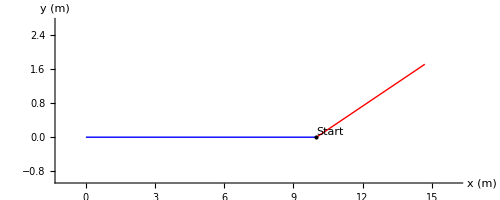

```mathematica
zacetekKlančine={ravnina,0};
konecKlančine=zacetekKlančine+d*{Cos[kot],Sin[kot]};

Graphics[{Thick,Blue,Line[{{0,0},{ravnina,0}}],Red,Line[{zacetekKlančine,konecKlančine}],Black,PointSize[Large],Point[zacetekKlančine],Text["Start",zacetekKlančine,{-1,-1}]},Axes->True,AspectRatio->Automatic,PlotRange->{{-1,ravnina+d+1},{-1,d*Sin[kot]+1}},AxesLabel->{"x (m)","y (m)"}]
```

c) Na sliko dodaj kroglico tako, da se bo kroglica premaknila, če se spremeni njeno središče (Uporabi `Dynamic`).

```mathematica
r=0.2;
kot=20*Pi/180;
d=5;
ravnina=10;

Manipulate[Graphics[{Thick,Blue,Line[{{0,0},{ravnina,0}}],Red,Line[{{ravnina,0},{ravnina+d*Cos[kot],d*Sin[kot]}}],Orange,Disk[{x,y},r]},Axes->True,AspectRatio->Automatic,PlotRange->{{-1,ravnina+d+1},{-1,d*Sin[kot]+1}},AxesLabel->{"x (m)","y (m)"}],{{x,2,"x"},0,ravnina+d},{{y,r,"y"},0,d*Sin[kot]+1}]
```

d) Definiraj funkcijo `naKlancu`, ki sprejme središče kroglice in vrne `True`, če je kroglica na klancu.

```mathematica
naklon=20 Degree;
dolzinaKlanca=5;
naKlancu[{x_,y_}]:=Module[{l},l=x Cos[naklon]+y Sin[naklon];
0<=l<=dolzinaKlanca]
```

e) Definiraj funkcijo `posodobiHitrost`, ki sprejme vektor trenutne hitrost kroglice in kot α ter vrne novo hitrost, gibanja po klančini z naklonom α po času Δt.

```mathematica
g=9.81
posodobiHitrost[hitrost_,alpha_,Δt_]:=Module[{pospesek},pospesek=g Sin[alpha] {Cos[alpha],Sin[alpha]};
hitrost+pospesek Δt]
```

9.81

f) Definiraj funkcijo `hitrostNaKlanec`, ki sprejme vektor trenutne hitrosti kroglice in kot α ter vrne novo hitrost, ki jo dobi kroglica, ko iz ravnega dela preide na klanec z naklonom α.

```mathematica
hitrostNaKlanec[hitrost_,alpha_]:=Module[{d,vproj},d={Cos[alpha],Sin[alpha]};
vproj=(hitrost.d) d;vproj]
```

g) Definiraj funkcijo `posodobiHitrostPosevniMet`, ki sprejme trenutno hitrost kroglice in vrne novo hitrost kroglice po času Δt.

```mathematica
g=9.81;
Δt=0.001;

posodobiHitrostPosevniMet[hitrost_]:=Module[{vx,vy},{vx,vy}=hitrost;
{vx,vy-g*Δt}]
```

h) Definiraj funkcijo `posodobiLego`, ki sprejme trenutno lego kroglice in njeno hitrost in vrne novo lego kroglice po času Δt.

```mathematica
Δt=0.001;

posodobiLego[lega_,hitrost_]:=lega+Δt*hitrost
```

i) S pomočjo prejšnjih funkcij simuliraj premikanje kroglice. (4 točke - gibanje po ravnini (1 točka), gibanje po klančini (1 točka), gibanje pri poševnem metu (1 točka), simulacija se ustavi, ko žogica pristane na tleh (1 točka))

```mathematica
g=9.81;
Δt=0.001;
r=0.2;
kot=20*Pi/180;
d=5;
ravninaDolzina=10;
v0=11;

posodobiHitrostPosevniMet[hitrost_]:=Module[{vx,vy},{vx,vy}=hitrost;
{vx,vy-g*Δt}]

posodobiLego[lega_,hitrost_]:=lega+Δt*hitrost
```